# Estimate Groundstate Decay from Exponential

```mathematica
<<ModList.m
<<StylePlot.m
```

```mathematica
Ratio={{1,2200}, {10,2500},{50,3000},{100,5000},{500,18000}}
```

{{1,2200},{10,2500},{50,3000},{100,5000},{500,18000}}

```mathematica
InvRatio=Map[{#[[1]],1/#[[2]]}&,Ratio]//N
LogInvRatio=Map[{#[[1]],-Log[1/#[[2]]]}&,Ratio]//N
```

{{1.,0.000454545},{10.,0.0004},{50.,0.000333333},{100.,0.0002},{500.,0.0000555556}}

{{1.,7.69621},{10.,7.82405},{50.,8.00637},{100.,8.51719},{500.,9.79813}}

```mathematica
line = Fit[LogInvRatio, {1,x},x]
```

7.83607+0.00402663 x

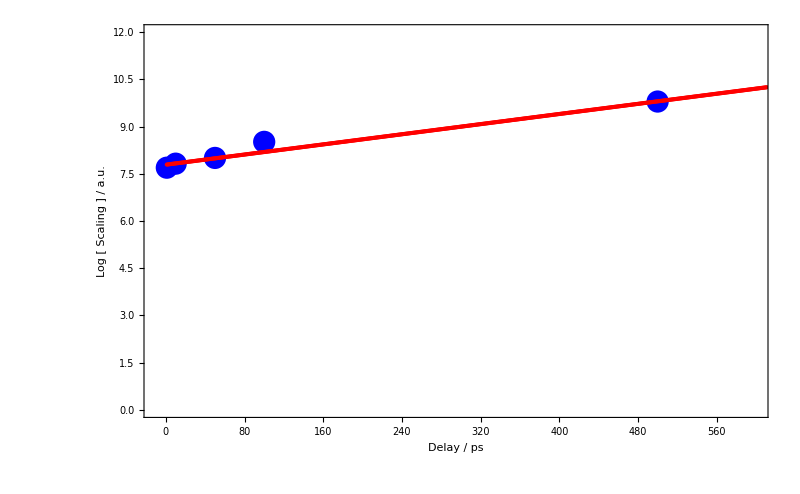

```mathematica
ListPlot[{LogInvRatio,Table[line,{x,-10,600}]},
PlotRange->{{-10,600},{0.,12}},
PlotStyle->{{Blue,PointSize[0.02]},Red},
FrameStyle->Directive[Black,25],
Frame->True,
FrameLabel->{{"Log [ Scaling ] / a.u.",""},{"Delay / ps",""}},
PlotTheme->{"Classic"},
ImageSize->800]
```

```mathematica
Manipulate[ListPlot[{InvRatio,Table[b+a Exp[-k x],{x,-1,600}]},
PlotRange->{{-10,600},{0.,0.0005}},
PlotStyle->{{Blue,PointSize[0.02]},Red},
FrameStyle->Directive[Black,25],
Frame->True,
FrameLabel->{{"Scaling / a.u.",""},{"Delay / ps",""}},
PlotTheme->{"Classic"},
ImageSize->800
],{{a,0.0004},0,0.001},{{k,0.007},0,0.5},{{b,0.00003},0,0.001}]
```

```mathematica
1/0.007
```

142.857

```mathematica
1/0.004
```

250.

# Export

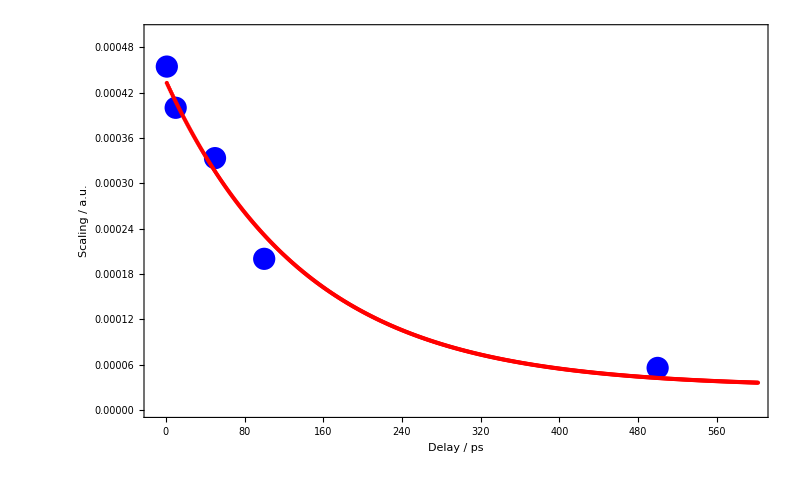
```mathematica
SetDirectory[NotebookDirectory[]]
Export["LinearFit.pdf",-Graphics-]
Export["ExpFit.pdf",-Graphics-]
```

/home/lindorfer/Post-Doc/TRCD/Spectra

LinearFit.pdf

ExpFit.pdf